```mathematica
Zdol=((s*L)^-1+s*c +1/r2)^-1
```

1/(0.617284+50.813/s+2.2×10^-6 s)

```mathematica
k=FullSimplify[Zdol/(Zdol+R)]
```

(293.255 s)/(2.30968×10^7+s (280877.+1. s))

```mathematica
impulseresponse=Simplify[InverseLaplaceTransform[k, s, t]]
```

293.341 ⅇ^(-280795. t)-0.0859305 ⅇ^(-82.2552 t)

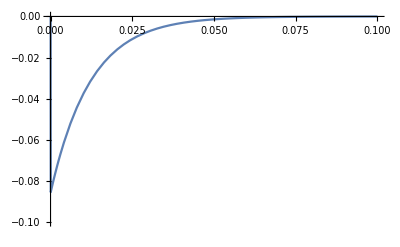

```mathematica
Plot[impulseresponse,{t, 0, 0.1}, PlotRange->{-0.10,0}]
```

```mathematica
stepresponse=Simplify[InverseLaplaceTransform[k/s, s, t]]
```

-0.00104468 ⅇ^(-280795. t)+0.00104468 ⅇ^(-82.2552 t)

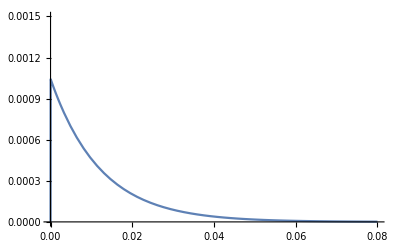

```mathematica
Plot[stepresponse,{t, 0,0.08}, PlotRange->{0,0.0015}]
```

```mathematica
R=1550
```

1550

```mathematica
r2=1.62
```

1.62

```mathematica
c=2.2*10^-6
```

2.2×10^-6

```mathematica
L=19.68*10^-3
```

0.01968

```mathematica
transmittance=Simplify[(293.2551319648094*I*w)/(2.309682187730968*^7+I*w(280876.869048912+1. I*w))]
```

((0.+293.255 ⅈ) w)/(2.30968×10^7+ⅈ (280877.+(0.+1. ⅈ) w) w)

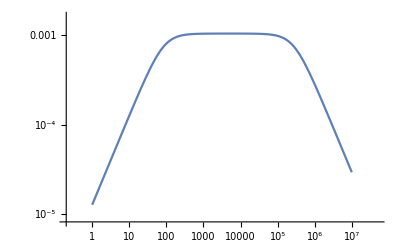

```mathematica
LogLogPlot[Abs[transmittance], {w, 1, 10000000}]
```

```mathematica
(L2 r2 w)/(-ⅈ r2 (R+Rg)+L2 (R+r2+Rg) w+C3 i L2 r2 (R+Rg) w^2)
```

(L2 r2 w)/(-ⅈ r2 (R+Rg)+L2 (R+r2+Rg) w+C3 i L2 r2 (R+Rg) w^2)

```mathematica
(w^2-2.30968*10^7)^2+(280877w)^2
```

78891889129 w^2+(-2.30968×10^7+w^2)^2

```mathematica
Expand[78891889129 w^2+(-2.30968*^7+w^2)^2]
```

5.33462×10^14+7.88457×10^10 w^2+w^4